```mathematica
(*zad1*)
m1 = {{1,2,0}, {-1,1,0}, {0,1,2}};
m2 = {x,y, z};
m3 = {3,1 , 3};
Solve[m1.m2==m3]
```

{{x→1/3,y→4/3,z→5/6}}

```mathematica
(*zad2*)
m11 = {{1,-2,3}, {2,3,-1}};
m22 = {x,y, z};
m33 = {1 , 5};
Solve[m11.m22==m33, {z,x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→13/7-z,y→3/7+z}}

```mathematica
(*zad3*)
(*a*)
Limit[E^x/(x^3-x+2),x-> Infinity]
```

∞

```mathematica
(*b*)
Limit[E^(1/(x^2-1)),x-> 1, Direction->"FromAbove"]
```

∞

```mathematica
(*c*)
Limit[E^(1/(x^2-1)),x-> 1, Direction->"FromBelow"]
```

0

```mathematica
(*d*)
Integrate[Sin[x]/x,{x,0, Infinity}]
```

π/2

```mathematica
(*e*)
f[x_, y_]:=(x^3*Sin[x*y])/(Cos[x^2+x*y]);
Simplify[D[f[x,y], {x,2}, {y,3}]]
```

1/2 x^4 Sec[x (x+y)]^6 (6 (15+86 x^4+88 x^3 y+22 x^2 y^2) Cos[x^2]-2 (-15+146 x^4+124 x^3 y+26 x^2 y^2) Cos[x (x+2 y)]+30 Cos[x (3 x+2 y)]-132 x^4 Cos[x (3 x+2 y)]-168 x^3 y Cos[x (3 x+2 y)]-52 x^2 y^2 Cos[x (3 x+2 y)]-15 Cos[x (3 x+4 y)]+18 x^4 Cos[x (3 x+4 y)]+12 x^3 y Cos[x (3 x+4 y)]+2 x^2 y^2 Cos[x (3 x+4 y)]-15 Cos[x (5 x+4 y)]+2 x^4 Cos[x (5 x+4 y)]+4 x^3 y Cos[x (5 x+4 y)]+2 x^2 y^2 Cos[x (5 x+4 y)]-78 x^2 Sin[x^2]+286 x^2 Sin[x (x+2 y)]+120 x y Sin[x (x+2 y)]+234 x^2 Sin[x (3 x+2 y)]+120 x y Sin[x (3 x+2 y)]-39 x^2 Sin[x (3 x+4 y)]-12 x y Sin[x (3 x+4 y)]-13 x^2 Sin[x (5 x+4 y)]-12 x y Sin[x (5 x+4 y)])

```mathematica
(*zad4*)
DSolve[y'[x]==y[x]x,y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
(*zad5*)
z5 = DSolve[{y'[x]==y[x]x,y[1]==2},y[x],x]
```

{{y[x]→2 ⅇ^(-1/2+x^2/2)}}

```mathematica
z5/.x-> 1
```

{{y[1]→2}}

```mathematica
z5/.x-> (7/2)
```

{{y[7/2]→2 ⅇ^(45/8)}}

{{y[x,t]→Cos[1/2 (2 t-x)]}}

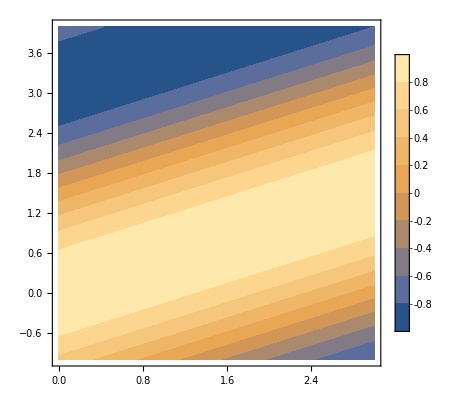

```mathematica
(*zad6*)
z6 = 2*D[y[x,t],x]+D[y[x,t],t];
res=DSolve[{z6==0, y[0,t]== Cos[t]},y[x,t],{x,t}]
ContourPlot[Evaluate[y[x,t]/.res], {x, 0, 3}, {t, -1,4}, Axes->True, PlotLegends->Automatic, ContourStyle->None]
```

```mathematica
(*zad7*)
ap = Normal[Series[Exp[x],{x,0,5}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

```mathematica
app[x_]:=Normal[Series[Exp[z],{z,0,5}]]/.z->x
```

```mathematica
app[2] // N
```

7.26667

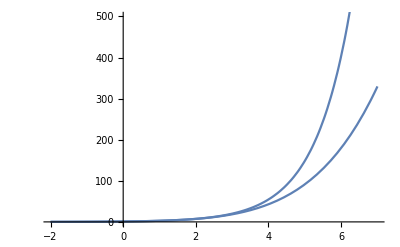

```mathematica
Show[
Plot[E^x, {x,-2, 7}],
Plot[app[x] , {x,-2, 7}],
PlotRange->{0, 500}
]
```

Piecewise[{{3, x≤0}, {1+x^2, x>0}, {0, True}}]

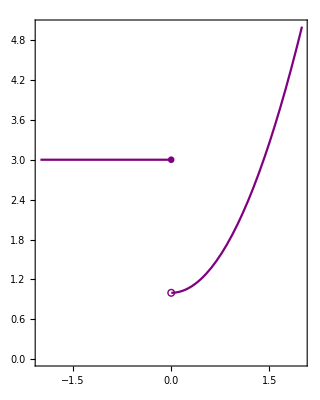

```mathematica
(*zad8*)
(*zad9*)
fw[x_]=Piecewise[{{3,x≤0},{x^2+1,x>0}}]
Show[
Plot[fw[x],{x,-2,2}, AxesOrigin->{0,0},AspectRatio->Automatic, Frame->True,Axes->None, PlotStyle->Purple],Graphics[{Purple,Circle[{0,1},0.05]}],
Graphics[{Purple,Disk[{0,3},0.05]}]]
```